{{10,0.175},{25,0.234},{50,0.522},{75,1.166},{100,2.189}}

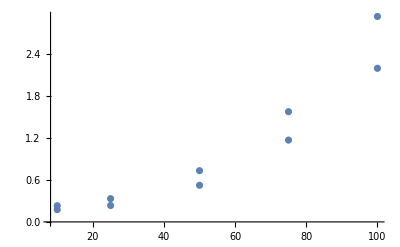

```mathematica
SetDirectory["C:\\Users\\Damian\\Desktop\\Masters\\CUDA\\FlowEquationSolver\\data"];
data1=Import["time15.txt", "CSV"];
data2=Import["time20.txt", "CSV"];
Show[{ListPlot[data2,PlotRange->Full],ListPlot[data1,PlotRange->Full]}]
```

```mathematica
Table[data2[[i]]-data1[[i]],{i,1,5}]
```

{{0,0.056},{0,0.097},{0,0.208},{0,0.405},{0,0.739}}